```mathematica
Mpl=2 10^18;
```

```mathematica
HubblePiecewise[T_,TR_,m_]:=Piecewise[{{TR^3/(T Mpl),m≤ T&&T≤ TR},{(TR^3 m^3)/(Mpl T^4),T≤ m}}]
HubbleRD[T_]:=T^2/Mpl;
AxionMass[T_,fa_,n_]:=6 10^-9 10^6/fa Piecewise[{{(0.1/T)^n,T>0.1},{1,T<0.1}}]
```

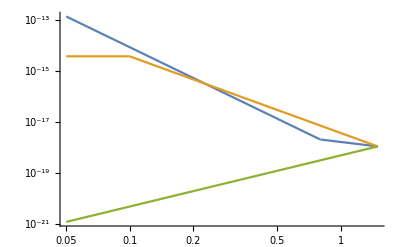

```mathematica
LogLogPlot[{HubblePiecewise[T,1.5,0.8],AxionMass[T,10^12.198724950769218,3],HubbleRD[T]},{T,0.05,1.5}]
```

```mathematica
TRtemp=1.5;
mStemp=1;
nTemp=3;
logfaTemp=FindRoot[HubblePiecewise[TRtemp,TRtemp,mStemp]==AxionMass[TRtemp,10^logfa,nTemp],{logfa,12}][[1,2]]
ToscTemp=FindRoot[HubblePiecewise[T,TRtemp,mStemp]==AxionMass[T,10^logfaTemp,nTemp],{T,0.2}][[1,2]]
(mStemp/ToscTemp)^(-4+3/2)(TRtemp/mStemp)^(-1+3/2)
```

12.1987

0.444444

0.161283

```mathematica
faSol=Solve[TR^2/Mpl==6 10^-9 10^6/fa(0.1/TR)^n,fa][[1,1,2]];
ToscSol=Solve[(TR^3 m^3)/(Mpl T^4)==6 10^-9 10^6/faSol(0.1/T)^n,T][[1,1,2]];
RatioSol=(m/ToscSol)^(-4+n/2)(TR/m)^(-1+n/2)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(TR/m)^(-1+n/2) (1.^(-1-1/(-4.+n)) m ((0.1^n 10.^(1. n) TR^(-1.+n))/m^3)^(-1/(-4.+n)))^(-4+n/2)

```mathematica
FullSimplify[RatioSol/.{n->1}]
```

1./(((1/m^3)^0.333333 m)^(7/2) √(TR/m))

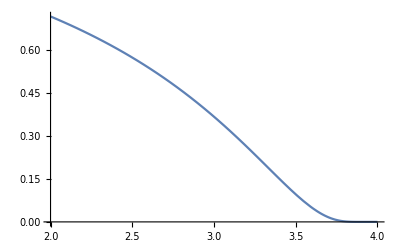

```mathematica
Plot[RatioSol/.{TR-> 1.5,m-> 1.2},{n,2,4}]
```

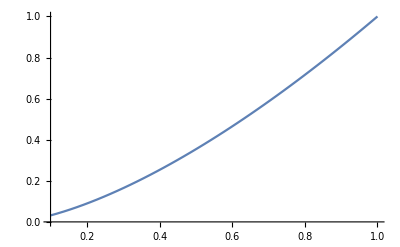

```mathematica
Plot[RatioSol/.{TR-> 1,n-> 2},{m,0.1,1}]
```